# von Nuemann - Analytic page curves bounds when all modes are initially squeezed equally

```mathematica
Remove["Global`*"];
```

```mathematica
SetOptions[Plot,BaseStyle->{FontSize->16}];
```

## Renyi-2

### Maximum renyi-2

```mathematica
S2max[s_,r_]:=Min[r,1-r]Log@Cosh[2s];
```

### Analytic page curve up to order r^dmax

```mathematica
S2[s_,r_,dmax_:20]:=With[{t2=Tanh[2s]^2,m=Min[r,1-r]},
m Log@Cosh[2s]+∑_(d=2)^dmax m^d∑_(l=Ceiling[d/2])^(d-1) (-1)^(d-l)/l t2^l Binomial[2l-1,l-1]Binomial[l,d-l-1](2l-d+1)/((d-1)d)
];
```

### Exact result for when r=1/2

```mathematica
S2half[s_]:=Log@Cosh@s;
```

### Max renyi-2 minus average renyi-2 at r=1/2

```mathematica
pageCorrection[s_]:=1/2 Log[1+Tanh[s]^2];
```

## von Nuemann

```mathematica
S1max[s_,r_]=With[{ν=Cosh[2s]},Min[r,1-r]((ν+1)/2 Log[(ν+1)/2]-(ν-1)/2 Log[(ν-1)/2])];
```

## Plots

```mathematica
plot[s_,dmax_:20]:=Plot[
{
S1max[s,r],S2[s,r,dmax],S2[s,r,dmax]+Min[r,1-r](1-Log@2)
},
{r,0,1},
PlotRange->All,
AxesLabel->{"r",None},
PlotLegends->{"1/n×max Renyi-1","1/n×average Renyi-2 = lower bound","1/n×average Renyi-2 + min(r,1-r)(1-Log2) = upper bound"},
PlotLabel->"Squeezing s = "<>ToString@s,
ImageSize->Large
];
```

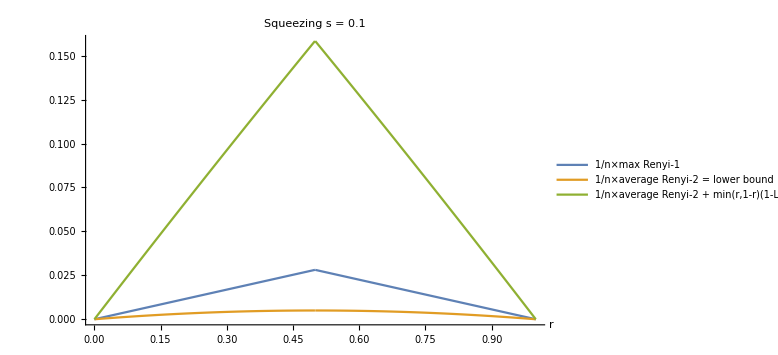
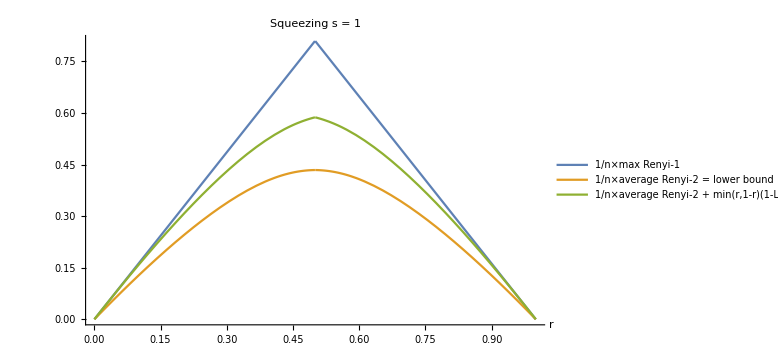
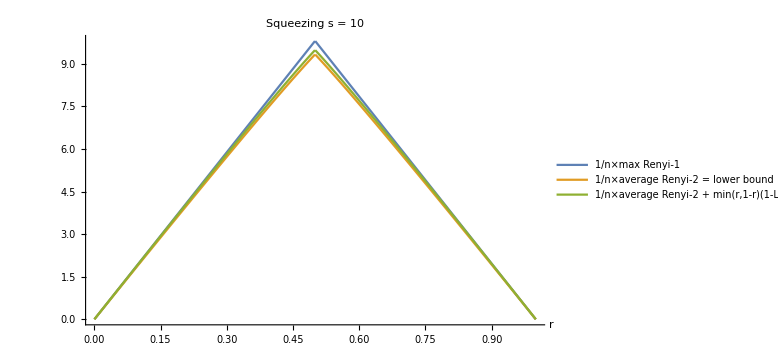

```mathematica
Table[plot[s],{s,{.1,1,10}}]//TableForm
```

```mathematica
Animate[plot[s],{s,0,5}]
```

### Export gif

```mathematica
(*SetDirectory@NotebookDirectory[];
Export[
"animated-plots.gif",
Table[plot@s,{s,Range[0,5,.15]},AnimationRepetitions->∞]
];*)
```